# Bifurcations

Bifurcations are where the stable points of a system change appear and disappear or change in character as a result of a parameter change.
There are a number of different types of these and we will explore some of the prototypical examples of each.

## Set up our graphics tooling.

We’re going to want to draw two plots, the phase plot of position against velocity, where we can identify the fixed points for a specific value of a parameter.
And the bifurcation plot where we draw where the fixed points are and what their character is for a varying parameter.

```mathematica
phasePlot=f↦Manipulate[
Quiet@Module[{
sign=D[f,x]>0,
nodes=Sort@Select[#∈Reals&]@
(x/.NSolve[f==0,x])
},
Plot[f,{x,-3,3},PlotRange->{-5,5},
Epilog->{
Red,
Arrowheads[{0,0,Automatic,0,Automatic}],
Thick,
Arrow[If[(f/.x->(#[[1,1]]+#[[2,1]])/2)>=0,Identity,Reverse][#]&/@Partition[{#,0}&/@Join[{-3},nodes,{3}],2,1]],
PointSize[Large],
Black,
Point[Map[{#,0}&]@Select[Not[sign/.(x->#)]&]@nodes],
Point[Map[{#,0}&]@Select[sign/.(x->#)&]@nodes],
White,
Point[Map[{#,0}&]@Select[sign/.(x->#)&]@nodes]
},AxesLabel->{"x", "dx/dt"}
]
],
{r,-3,3}
];
bifurcationPlot=f↦Module[
{
sign=D[f,x]>0
},
Show[
ContourPlot[If[sign,1,Null]f==0,{r,-3,3},{x,-3,3},ContourStyle->Dashed,FrameLabel->{"Control Parameter – r","Fixed Points – x^*"},GridLines->{{0},{0}}],
ContourPlot[If[sign,Null,1]f==0,{r,-3,3},{x,-3,3}]
]
];
```

## Saddle Node Bifurcation

Also called fold bifurcation or blue sky bifurcation. This is where two fixed points spontaneously appear, one stable and one unstable.
In a 1D system with a continuous velocity function, the “charge” of fixed points is conserved and attracting and repelling fixed points are created or annihilated in pairs.
This bifurcation will also appear in some of the more complex examples.
Here x is our dynamic variable and r is a control parameter.

r+x^2

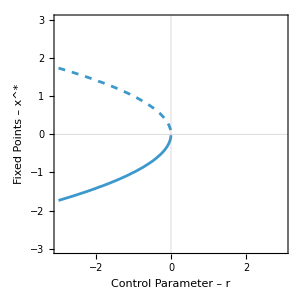

```mathematica
r +x^2
phasePlot[%]
bifurcationPlot[%%]
```

## Transcritical Bifurcation

In a transcritical bifurcation, two fixed points pass through each other and exchange their criticality as they do so.
We saw this in the 2D case with the logistic predator-prey system.

r x-x^2

r x (1-x/r)

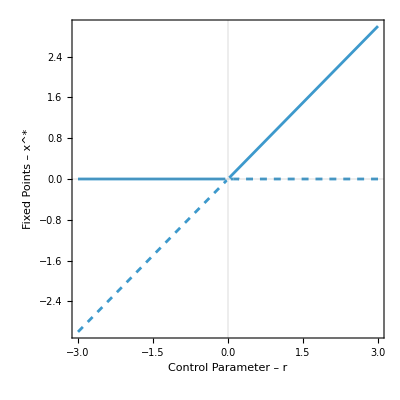

```mathematica
r x -x^2
r x(1-x/r)
phasePlot[%]
bifurcationPlot[%%]
```

## Pitchfork Bifurcation

### Supercritical

This bifurcation is related to spontaneous symmetry breaking, i.e. your system is symmetric in x, but you can end up that the state converges to a non-zero value based on initial conditions.
The typical example is a beam buckling under stress, it can buckle left or right, and will be unstable down the middle until it is perturbed in one of the directions.

r x-x^3

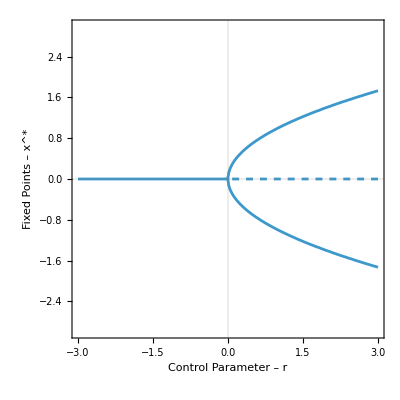

```mathematica
r x -x^3
phasePlot[%]
bifurcationPlot[%%]
```

### Subcritical

In principal a subcritical bifurcation is just the opposite of a supercritical one, however having unstable fixed points that aren’t bracketed by stable ones leads to trajectories that diverge to infinity. Usually a physical effect will stop trajectories diverging, so the subcritical example uses a 5th order polynomial to “contain” the divergent fixed points.
Observe we have saddle-node bifurcations here too when r=0.25. And the pitchfork bifurcation around r=0.

r x+x^3-x^5

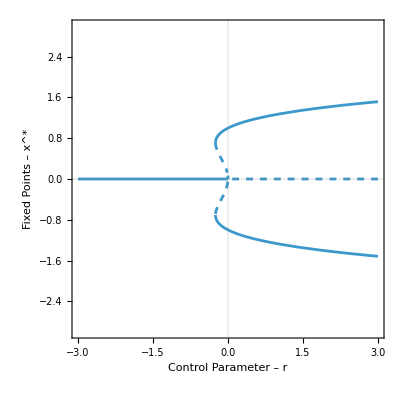

```mathematica
r x +x^3-x^5
phasePlot[%]
bifurcationPlot[%%]
```

### Imperfect and Catastrophe

If we have a bias in the system, we set a preferred fixed point of the system. The branches disconnect in a saddle-node bifurcation.
This system has two stable points for large values of the control parameter, but one of those branches can disappear as the parameter is reduced.
The switching from a favoured fixed point to a unfavourable one, e.g. from low value of x^* to a high one, and being unable to recover by tuning parameters is referred to as a catastrophe.
In this case a cusp-catastrophe, as the region in h-r parameter space where two values are stable is bounded by a cusped curve.

```mathematica
r x -x^3+h
Manipulate[
bifurcationPlot[%],
{{h,0.1},-3,3}
]
```

h+r x-x^3

```mathematica
x/.Solve[r x -x^3+h==0,x]//FullSimplify;
Plot3D[%,{r,-3,3},{h,-3,3},PlotPoints->100,Mesh->None,AxesLabel->{"Control Parameter – r", "Bias Parameter – k", "Fixed Points – x^*"},PlotRange->Full,PlotStyle->{Directive[{Opacity[0.5],White}],Directive[{Opacity[0.5],White}],Directive[{Opacity[0.05],White}]}]
```

-Graphics3D-

### Insect Outbreak

The model we considered in class (Treated on pg. 74 in Strogatz) had logistic growth for an insect population with saturated slow-onset predation from a bird species.
We can draw new bifurcation diagrams for each parameter.
We see that we are able to transition from a region where a low refuge insect population is stable to one where both outbreak and refuge are stable to a region where only refuge is stable.
In this case we can end up not being able to easily return to the pre-outbreak catastrophe refuge state.

```mathematica
bifurcationPlot2=f↦Module[
{
sign=D[f,x]>0
},
Show[
ContourPlot[If[sign,1,Null]f==0,{r,0,1},{x,0,15},ContourStyle->Dashed,FrameLabel->{"Normalised Growth Rate – r","Fixed Points – x^*"}],
ContourPlot[If[sign,Null,1]f==0,{r,0,1},{x,0,15}]
]
];
bifurcationPlot3=f↦Module[
{
sign=D[f,x]>0
},
Show[
ContourPlot[If[sign,1,Null]f==0,{k,0,15},{x,0,15},ContourStyle->Dashed,FrameLabel->{"Normalised Carrying Capacity – k","Fixed Points – x^*"}],
ContourPlot[If[sign,Null,1]f==0,{k,0,15},{x,0,15}]
]
];
Manipulate[
bifurcationPlot2[r x(1-x/k)-x^2/(1+x^2)],
{{k,10},0,15}
]
Manipulate[
bifurcationPlot3[r x(1-x/k)-x^2/(1+x^2)],
{{r,0.54},0,1}
]
```

We can also plot the cusp in a 3D plot with both parameters.

```mathematica
x/.Solve[r x(1-x/k)-x^2/(1+x^2)==0,x];
Plot3D[%,{r,0,1},{k,0,15},PlotRange->Full,PlotPoints->100,PlotStyle->{Directive[{Opacity[0.05],White}],Directive[{Opacity[0.5],White}],Directive[{Opacity[0.5],White}],Directive[{Opacity[0.05],White}]},Mesh->None,AxesLabel->{"r", "k", "x^*"}]
```

-Graphics3D-

#### Simulation

Let’s run a simulation, we’ll start with parameters of r=0.54 and k=12 and an initial value of x=0.5.
We’ll use the Runge-Kutta-Fehlberg machinery that we’ve previously developed.
In this case, after 100 units of time, we’ll transition the value of k to 20, then at 200 units of time, transition back to k=12.

```mathematica
updateRKF45prime=Function[{f,tol},Function[state,
Module[{k1,k2,k3,k4,k5,k6,y1,y2,y3,y4,y5,y6,t,yNext,yHat,α,β,c,cHat,cTE,h,TE,hNext},
β=N[{{2/9, 0, 0, 0, 0}, {1/12, 1/4, 0, 0, 0}, {69/128, -243/128, 135/64, 0, 0}, {-17/12, 27/4, -27/5, 16/15, 0}, {65/432, -5/16, 13/16, 4/27, 5/144}}];
α=Total/@β;
c={1/9,0,9/20,16/45,1/12,0};
cHat={47/450,0,12/25,32/225,1/30,6/25};
cTE=c-cHat;
t=state[[1]];
y1=state[[2]];
h=state[[3]];
k1=Apply[f[t],y1];
y2=y1+β[[1,1]]h k1;
k2=f[t+α[[1]]h]@@y2;
y3=y1+β[[2,1]]h k1+β[[2,2]]h k2;
k3=f[t+α[[2]]h]@@y3;
y4=y1+β[[3,1]]h k1+β[[3,2]]h k2+β[[3,3]]h k3;
k4=f[t+α[[3]]h]@@y4;
y5=y1+β[[4,1]]h k1+β[[4,2]]h k2+β[[4,3]]h k3+β[[4,4]]h k4;
k5=f[t+α[[4]]h]@@y5;
y6=y1+β[[5,1]]h k1+β[[5,2]]h k2+β[[5,3]]h k3+β[[5,4]]h k4+β[[5,5]]h k5;
k6=f[t+α[[5]]h]@@y6;
yNext=y1+h c[[1]]k1+h c[[2]]k2+h c[[3]]k3+h c[[4]]k4+h c[[5]]k5;
yHat=y1+h cHat[[1]]k1+h cHat[[2]]k2+h cHat[[3]]k3+h cHat[[4]]k4+h cHat[[5]]k5+h cHat[[6]] k6;
TE=h cTE[[1]]k1+h cTE[[2]]k2+h cTE[[3]]k3+h cTE[[4]]k4+h cTE[[5]]k5+h cTE[[6]] k6;
hNext=0.9h(tol/Max[Abs[TE]])^(1/5);
If[
Max[Abs[TE]]>tol,
{t,y1,hNext,True},(* We'll mark results as True if they need to be repeated *)
{t+h,yHat,hNext,False} (* And False if they are good. Then we can NestWhile they need to be repeated. *)
]
]]];
updateRKF45={f,tol}↦state↦Most[NestWhile[updateRKF45prime[f,tol],Join[state,{True}],Last]];
```

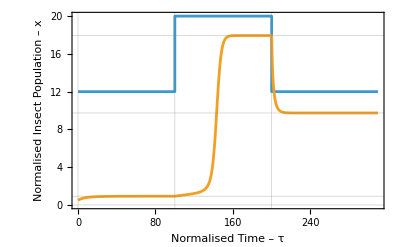

```mathematica
initialState={0,{0.5},0.1};
rr=t↦0.54;
kk=t↦Piecewise[{{12, t<100}, {20, t<200}, {12, True}}];
f=t↦x↦{rr[t] x(1-x/kk[t])-x^2/(1+x^2)};
step=updateRKF45[f,10^-6];
NestWhileList[step, initialState, s↦s[[1]]<300];
ListLinePlot[{Map[{#[[1]],kk[#[[1]]]}&,%],Map[{#[[1]],#[[2,1]]}&,%]},GridLines->{{0,100,200},{0,0.9237478148923517,9.742918851774316,17.942144353152504}},Frame->True,FrameLabel->{{"Normalised Insect Population – x","Normalised Carrying Capacity – k"},{"Normalised Time – τ", ""}}]
```

Here we start with the population nearby to the refuge stable point, to which it quickly converges. Once the carrying capacity is increased past the cusp catastrophe point the population rises to the new single attracting point. Restoring the carrying capacity does not return the system to previous level, it now converges to the higher outbreak level.

## References

Strogatz, Steven H. Nonlinear Dynamics and Chaos : With Applications to Physics, Biology, Chemistry, and Engineering. Second edition. Boca Raton, FL ; CRC Press, Taylor & Francis Group, 2018. Print.
Chapter 3